```mathematica
Get["BDetSpread/Definitions.m"]
```

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

# Electrons

### memoization

```mathematica
FitFuncMemoDetSpreadArith[
{b_,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_
]:=
FitFuncMemoDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]=
Reverse[IntTableDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
FitFuncBinNormDetSpreadArith[bin_?NumericQ,{b_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_]:=FitFuncMemoDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec][[bin]]/Total[FitFuncMemoDetSpreadArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

## 90° no filter, no Offset!

Data 90° no Filter

```mathematica
XDatam55p05Bins32=XDataCreation[{-0.055,0.005,0.},32]
```

{-0.055,-0.0530645,-0.051129,-0.0491935,-0.0472581,-0.0453226,-0.0433871,-0.0414516,-0.0395161,-0.0375806,-0.0356452,-0.0337097,-0.0317742,-0.0298387,-0.0279032,-0.0259677,-0.0240323,-0.0220968,-0.0201613,-0.0182258,-0.0162903,-0.0143548,-0.0124194,-0.0104839,-0.00854839,-0.0066129,-0.00467742,-0.00274194,-0.000806452,0.00112903,0.00306452,0.005}

```mathematica
t0=AbsoluteTime[];
ILLData90noFilter=Table[{bin,FitFuncBinNormDetSpreadArith[bin,{0.,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05Bins32,3]},{bin,1,Length[XDatam55p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14544 and 0.00554642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0346 and 0.00895122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.015101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0155815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94809 and 0.00517473 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72955 and 0.0121513 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.0367431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172851 and 0.000378845 for the integral and error estimates.

510.745854

### 510s

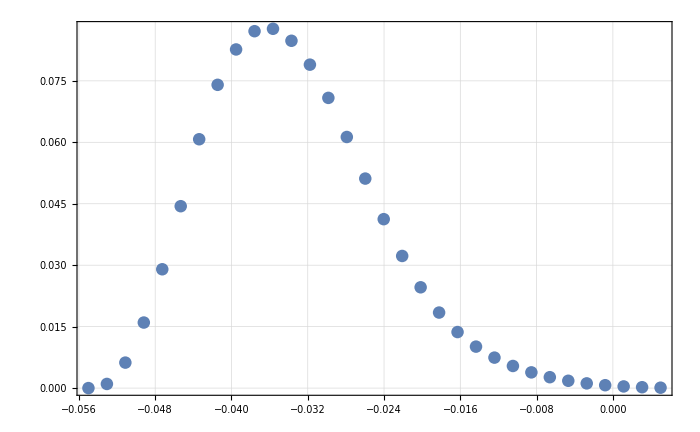

```mathematica
ListPlot[Transpose[{XDatam55p05Bins32,ILLData90noFilter[[All,2]]}]]
```

Fits

### drD fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drDFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormDetSpreadArith[bin,{b,Pi/2,0.2,1./2,1./2+1/2*10^-4,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 1 Jul 2019 17:39:42

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33349 and 0.00490071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14481 and 0.00555129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03385 and 0.00900082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4558 and 0.0153127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.026873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94858 and 0.00517799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72977 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06123 and 0.0367644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17283 and 0.000378118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3341 and 0.00490232 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1456 and 0.00545082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03523 and 0.0092398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94716 and 0.00517706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72886 and 0.0121532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06079 and 0.0367553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172736 and 0.000377901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33415 and 0.00490244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14565 and 0.00545096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03534 and 0.00923992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0152095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3612 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94706 and 0.00517698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72879 and 0.012153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172729 and 0.000377884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33407 and 0.00490224 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14556 and 0.00545074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03517 and 0.00923972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94723 and 0.0051771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000377911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3336 and 0.004901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14495 and 0.00555161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0341 and 0.00900112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.015313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3631 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94833 and 0.00517782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06115 and 0.0367627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7296 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172813 and 0.000378079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33408 and 0.00490226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14557 and 0.00545076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03519 and 0.00923974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94721 and 0.00517709 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72889 and 0.0121533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.0367556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172739 and 0.000377908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33295 and 0.00489928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14412 and 0.00554971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03261 and 0.0090419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4545 and 0.015311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0268743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8635 and 0.0157715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3654 and 0.0104236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94984 and 0.00517882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73057 and 0.0121588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06161 and 0.0367725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172913 and 0.000378312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3341 and 0.0049023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14559 and 0.00545081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03522 and 0.00923979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94718 and 0.00517706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72887 and 0.0121532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06079 and 0.0367553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172737 and 0.000377902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33318 and 0.00489988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1444 and 0.00555037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03288 and 0.00924792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.455 and 0.0153117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8631 and 0.0157709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3646 and 0.010421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94932 and 0.00517848 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73024 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06145 and 0.0367691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172879 and 0.000378231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33291 and 0.00489916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14406 and 0.00554958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0325 and 0.00904178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0153109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0268744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8635 and 0.0157716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3656 and 0.0104237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94995 and 0.00517889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73064 and 0.012159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06165 and 0.0367732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172921 and 0.000378328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3341 and 0.00490232 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1456 and 0.00545082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03523 and 0.0092398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94716 and 0.00517706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72886 and 0.0121532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06079 and 0.0367553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172736 and 0.000377901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33311 and 0.0048997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14432 and 0.00555018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03274 and 0.00924775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4549 and 0.0153115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.026874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8632 and 0.0157711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3649 and 0.0104234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94947 and 0.00517858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73034 and 0.012158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.000378255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33362 and 0.00490105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14497 and 0.00555166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03414 and 0.00900117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94829 and 0.0051778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72958 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0367625 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17281 and 0.000378073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33349 and 0.0049007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1448 and 0.00555127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03384 and 0.0090008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4558 and 0.0153126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94859 and 0.005178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72977 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06123 and 0.0367645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172831 and 0.00037812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.0049022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14554 and 0.0054507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03514 and 0.00923968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94727 and 0.00517712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172743 and 0.000377916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33416 and 0.00490248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14567 and 0.005451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.00923996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0152095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94702 and 0.00517696 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72877 and 0.0121529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06074 and 0.0367544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172727 and 0.000377879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33354 and 0.00490082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14486 and 0.00555141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03394 and 0.00900093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0153128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00517793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72971 and 0.012156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0612 and 0.0367638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172824 and 0.000378104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33298 and 0.00489935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14415 and 0.00554979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03244 and 0.0092474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4545 and 0.0153111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0268743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8634 and 0.0157714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3654 and 0.0104236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94978 and 0.00517878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73053 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06159 and 0.0367721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172909 and 0.000378302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33288 and 0.00489909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14403 and 0.0055495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03244 and 0.00904171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0153108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0268745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8636 and 0.0157716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3657 and 0.0104237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95001 and 0.00517893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73068 and 0.0121592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06167 and 0.0367736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172925 and 0.000378338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33392 and 0.00490184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14536 and 0.0054503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03481 and 0.00900199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0152751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.026872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.362 and 0.0104198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94759 and 0.00517734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06092 and 0.036758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72913 and 0.0121541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172764 and 0.000377966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33333 and 0.00490028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1446 and 0.00555081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03348 and 0.00900037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0153122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3641 and 0.0104208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94896 and 0.00517824 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73001 and 0.012157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0367668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172855 and 0.000378176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33326 and 0.00490009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1445 and 0.0055506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03332 and 0.00900016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4552 and 0.0153119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0157707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3644 and 0.0104209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94913 and 0.00517836 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0614 and 0.036768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73012 and 0.0121573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172867 and 0.000378203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00490219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14554 and 0.00545069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03513 and 0.00923968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94727 and 0.00517713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72893 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.036756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172743 and 0.000377917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33341 and 0.00490048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1447 and 0.00555103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03365 and 0.00900057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0153124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0157704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94879 and 0.00517813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7299 and 0.0121566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172843 and 0.00037815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.0049018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14534 and 0.00545026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03478 and 0.00900195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0152751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.362 and 0.0104198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94762 and 0.00517736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06093 and 0.0367582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72915 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172766 and 0.000377971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33413 and 0.00490238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14563 and 0.00545089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03529 and 0.00923987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3613 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94711 and 0.00517702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172732 and 0.000377892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33413 and 0.0049024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14564 and 0.00545091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03531 and 0.00923988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0268715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3612 and 0.0108623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94709 and 0.00517701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72881 and 0.0121531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172731 and 0.000377889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33389 and 0.00490176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14533 and 0.00545022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03475 and 0.00900191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0152751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3621 and 0.0104198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94765 and 0.00517738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72917 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06094 and 0.0367584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172768 and 0.000377976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33409 and 0.00490228 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0352 and 0.00923976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0152757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0108624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9472 and 0.00517708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.0367555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172738 and 0.000377906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33375 and 0.00490139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14514 and 0.00555204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03443 and 0.00900153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0152746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.0367605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94798 and 0.00517759 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17279 and 0.000378026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00490222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14555 and 0.00545072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03515 and 0.0092397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0152756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0108625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94725 and 0.00517711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.0121534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172742 and 0.000377914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00490193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14541 and 0.0054504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0349 and 0.00923941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0152752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0268719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0157691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94751 and 0.00517728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72908 and 0.0121539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06089 and 0.0367575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172759 and 0.000377954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33374 and 0.00490135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14512 and 0.005552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0344 and 0.00900149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.0152746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94801 and 0.00517762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06105 and 0.0367607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7294 and 0.012155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172792 and 0.000378031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33365 and 0.00490112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.145 and 0.00555173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0342 and 0.00900124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0153131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94822 and 0.00517776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72954 and 0.0121554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06111 and 0.0367621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172806 and 0.000378063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33323 and 0.00490002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14447 and 0.00555052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03301 and 0.00924806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4552 and 0.0153118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0268737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.863 and 0.0157708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3644 and 0.010421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94919 and 0.00517839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73016 and 0.0121575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06141 and 0.0367683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17287 and 0.000378212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33368 and 0.00490121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14505 and 0.00555184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00900133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0153132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94814 and 0.0051777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06109 and 0.0367616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172801 and 0.000378051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33347 and 0.00490065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14478 and 0.00555122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03379 and 0.00900075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0153126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0268731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94864 and 0.00517803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7298 and 0.0121563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172834 and 0.000378127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33356 and 0.00490089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14489 and 0.00555149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.034 and 0.009001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0153129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0268729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8624 and 0.01577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94842 and 0.00517789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0367634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000378094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.89713 and 0.00373479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.58612 and 0.00401948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64543 and 0.010002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.04542 and 0.00818211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.40166 and 0.0138846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.8362 and 0.0150858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2352 and 0.0284775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.6252 and 0.0166665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.9683 and 0.00854892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.38236 and 0.0148182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37585 and 0.0427142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.240452 and 0.000534165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.89713 and 0.00373479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.58612 and 0.00401948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64543 and 0.010002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.04542 and 0.00818211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.40166 and 0.0138846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.8362 and 0.0150858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2352 and 0.0284775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.6252 and 0.0166665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.9683 and 0.00854892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.38236 and 0.0148182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37585 and 0.0427142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.240452 and 0.000534165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94808 and 0.00387148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6514 and 0.00416852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.74529 and 0.0102628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.16061 and 0.00820653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.5251 and 0.0142314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2625 and 0.0281273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.5362 and 0.0166171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.84917 and 0.00839432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.33908 and 0.0420831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.30631 and 0.0144514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23255 and 0.000517658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94808 and 0.00387148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6514 and 0.00416852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.74529 and 0.0102628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.16061 and 0.00820653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.5251 and 0.0142314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.2625 and 0.0281273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.5362 and 0.0166171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.84917 and 0.00839432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.30631 and 0.0144514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.33908 and 0.0420831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23255 and 0.000517658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33382 and 0.00490157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14524 and 0.00545002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3623 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00517749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000378001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000378009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000378009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.00037801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14521 and 0.00544995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03454 and 0.00900165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0152748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0268723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.01042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94787 and 0.00517752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06101 and 0.0367598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.00037801 for the integral and error estimates.

24858.24408

### took 24858s or 6.9h

```mathematica
drDFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000818071 | 0.0000910504 | -8.98481 | 3.87318×10^-10

```mathematica
drDFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

-8.18071

## 90° no filter

Data

```mathematica
OffsetXDatam55p05Bins32=XDataCreation[{-0.055,0.005,0.025},32]
```

{-0.03,-0.0280645,-0.026129,-0.0241935,-0.0222581,-0.0203226,-0.0183871,-0.0164516,-0.0145161,-0.0125806,-0.0106452,-0.00870968,-0.00677419,-0.00483871,-0.00290323,-0.000967742,0.000967742,0.00290323,0.00483871,0.00677419,0.00870968,0.0106452,0.0125806,0.0145161,0.0164516,0.0183871,0.0203226,0.0222581,0.0241935,0.026129,0.0280645,0.03}

```mathematica
t0=AbsoluteTime[];
OffsetILLData90noFilter=Table[{bin,FitFuncBinNormDetSpreadArith[bin,{0.,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.025,0.,0.},OffsetXDatam55p05Bins32,3]},{bin,1,Length[OffsetXDatam55p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14544 and 0.00554641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0346 and 0.0089512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0155815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94809 and 0.00517484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.0367432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72955 and 0.0121514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172851 and 0.000378797 for the integral and error estimates.

469.987439

### 470s

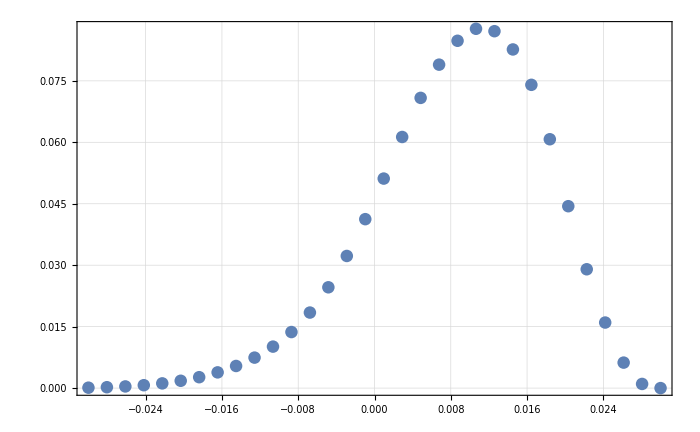

```mathematica
ListPlot[
Transpose[{Reverse[OffsetXDatam55p05Bins32],OffsetILLData90noFilter[[All,2]]}]
]
```

Fits

### drD fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drDFitOffset=Reap[NonlinearModelFit[
OffsetILLData90noFilter,
{
FitFuncBinNormDetSpreadArith[bin,{b,Pi/2,0.2,1./2,1./2+1/2*10^-4,1.,1/2.},{0.01,0.035,0.025,0.,0.},OffsetXDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Tue 2 Jul 2019 14:23:01

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00491364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14542 and 0.00543934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03484 and 0.00895131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8624 and 0.0154523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94701 and 0.00511432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72856 and 0.0121179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06061 and 0.0367704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172559 and 0.0003772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33456 and 0.00491525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14619 and 0.00545236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03621 and 0.00895297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.015451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94559 and 0.00511332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72766 and 0.0121067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06017 and 0.0367613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172465 and 0.000376982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.00491538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14625 and 0.0054525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03632 and 0.0089531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.0150559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.027143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3594 and 0.0104202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94549 and 0.00511325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72759 and 0.0121065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06014 and 0.0367606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172458 and 0.000376966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33453 and 0.00491518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14616 and 0.00545228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03615 and 0.00895289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8614 and 0.015451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3597 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94566 and 0.00511337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06019 and 0.0367617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7277 and 0.0121069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17247 and 0.000376993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00491393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14556 and 0.00545094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03509 and 0.00895161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0270944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94676 and 0.00511414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72839 and 0.0121174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06053 and 0.0367688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172542 and 0.000377161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33454 and 0.0049152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14617 and 0.0054523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03616 and 0.00895292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.015451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94564 and 0.00511336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72769 and 0.0121068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06019 and 0.0367616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172468 and 0.00037699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33342 and 0.00491221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14472 and 0.00554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03363 and 0.00899317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4555 and 0.0150523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8633 and 0.0154535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3637 and 0.0104563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94827 and 0.00511521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72936 and 0.0121205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.061 and 0.0367785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172642 and 0.000377393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33456 and 0.00491524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14619 and 0.00545235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0362 and 0.00895296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.015451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94561 and 0.00511333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72767 and 0.0121068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06018 and 0.0367614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172466 and 0.000376984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33364 and 0.0049128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.145 and 0.00554065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03414 and 0.00899379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.015053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0270954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8629 and 0.015453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3629 and 0.0104559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94775 and 0.00511484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72903 and 0.0121194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06084 and 0.0367752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172608 and 0.000377313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33337 and 0.00491209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14466 and 0.00553987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03353 and 0.00899305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0270961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8634 and 0.0154536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94838 and 0.00511528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72943 and 0.0121207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06103 and 0.0367792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17265 and 0.00037741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33456 and 0.00491525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14619 and 0.00545236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03621 and 0.00895297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.015451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94559 and 0.00511332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06017 and 0.0367613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72766 and 0.0121067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172465 and 0.000376983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33357 and 0.00491263 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14492 and 0.00554046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03399 and 0.00899361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0270956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.863 and 0.0154532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3631 and 0.010456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9479 and 0.00511495 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06088 and 0.0367762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72913 and 0.0121198 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172618 and 0.000377336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33408 and 0.00491398 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03513 and 0.00895166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0270943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.015452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94672 and 0.00511411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72837 and 0.0121173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06052 and 0.0367685 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172539 and 0.000377154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00491363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14541 and 0.00543933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03485 and 0.00899465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8624 and 0.0154523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94702 and 0.00511433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72857 and 0.0121179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06061 and 0.0367705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17256 and 0.000377201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33452 and 0.00491514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14614 and 0.00545224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03611 and 0.00895285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4581 and 0.0150556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4643 and 0.0271433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8614 and 0.0154511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3597 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9457 and 0.00511339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72772 and 0.0121069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0602 and 0.036762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172472 and 0.000376998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33433 and 0.00491465 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1459 and 0.00545171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00895235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4642 and 0.0271437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3604 and 0.0104339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94613 and 0.0051137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72799 and 0.0121161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06034 and 0.0367647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172501 and 0.000377065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33345 and 0.0049123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14476 and 0.0055401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03371 and 0.00899327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0270959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8632 and 0.0154535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94819 and 0.00511515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06097 and 0.036778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172637 and 0.00037738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33334 and 0.00491202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14462 and 0.00553979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03347 and 0.00899298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0270962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8634 and 0.0154537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3639 and 0.0104564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94844 and 0.00511533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72947 and 0.0121209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06105 and 0.0367796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172653 and 0.000377419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33376 and 0.00491312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14516 and 0.005541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03441 and 0.00899412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0270951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8627 and 0.0154528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94747 and 0.00511464 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72885 and 0.0121188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172589 and 0.00037727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33413 and 0.00491411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14564 and 0.00545113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03524 and 0.00895179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0270942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9466 and 0.00511403 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06048 and 0.0367678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7283 and 0.012117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172532 and 0.000377137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491495 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14605 and 0.00545203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03595 and 0.00895266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.458 and 0.0150554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4642 and 0.0271434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.36 and 0.0104205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94586 and 0.00511351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72783 and 0.0121073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06025 and 0.036763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172483 and 0.000377024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33336 and 0.00491207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14465 and 0.00553984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03351 and 0.00899303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0270961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8634 and 0.0154537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3639 and 0.0104564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9484 and 0.0051153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72944 and 0.0121208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.0367793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172651 and 0.000377412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00491332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14526 and 0.00543899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03458 and 0.00899433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8626 and 0.0154526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9473 and 0.00511452 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0607 and 0.0367723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72874 and 0.0121185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172578 and 0.000377243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00491349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14534 and 0.00543918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03473 and 0.0089945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8625 and 0.0154525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94715 and 0.00511442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06065 and 0.0367713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172568 and 0.00037722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.0049135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14535 and 0.00543919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03473 and 0.00899451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8625 and 0.0154525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94714 and 0.00511441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06065 and 0.0367712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172567 and 0.000377219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00491421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14569 and 0.00545123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03532 and 0.00895189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0270941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.361 and 0.010455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94652 and 0.00511397 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06046 and 0.0367672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172526 and 0.000377124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33339 and 0.00491213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14468 and 0.00553992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03357 and 0.0089931 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0270961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8634 and 0.0154536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94834 and 0.00511526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72941 and 0.0121207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06102 and 0.036779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172647 and 0.000377403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33335 and 0.00491203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14463 and 0.0055398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03348 and 0.00899299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0270962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8634 and 0.0154537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3639 and 0.0104564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94843 and 0.00511532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06105 and 0.0367796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72947 and 0.0121209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172653 and 0.000377418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33338 and 0.0049121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14466 and 0.00553988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03354 and 0.00899306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0270961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8634 and 0.0154536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94837 and 0.00511528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06103 and 0.0367791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172649 and 0.000377407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33365 and 0.00491282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14501 and 0.00554067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03416 and 0.00899381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.015053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0270954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8629 and 0.015453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94773 and 0.00511483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72902 and 0.0121194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06083 and 0.0367751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172607 and 0.00037731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33376 and 0.00491314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14516 and 0.00554102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03443 and 0.00899414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0270951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8627 and 0.0154528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94746 and 0.00511463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72884 and 0.0121188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172588 and 0.000377268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00491341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14531 and 0.00543909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03466 and 0.00899442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8625 and 0.0154525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.0104555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94722 and 0.00511446 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72869 and 0.0121183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06067 and 0.0367717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172572 and 0.000377231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00491349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14535 and 0.00543918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03473 and 0.00899451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8625 and 0.0154525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94714 and 0.00511441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06065 and 0.0367713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172568 and 0.00037722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33402 and 0.00491382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1455 and 0.00545082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03499 and 0.00895149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0270945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94686 and 0.00511421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72846 and 0.0121176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06056 and 0.0367694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172549 and 0.000377176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.0049138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.1455 and 0.0054508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03497 and 0.00895148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0270945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94687 and 0.00511422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06057 and 0.0367695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72847 and 0.0121176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17255 and 0.000377178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33418 and 0.00491424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14571 and 0.00545127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.00895193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0270941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3609 and 0.010455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94649 and 0.00511395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72822 and 0.0121168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06045 and 0.036767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172524 and 0.000377119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33349 and 0.0049124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14481 and 0.0055402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03379 and 0.00899337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0270958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8632 and 0.0154534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00511509 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06095 and 0.0367775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72926 and 0.0121202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172632 and 0.000377368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00491332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14526 and 0.00543899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03458 and 0.00899433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0270949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8626 and 0.0154526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9473 and 0.00511452 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0607 and 0.0367723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72874 and 0.0121185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172578 and 0.000377243 for the integral and error estimates.

17896.89967

### took 17896s or 5h

```mathematica
drDFitOffset[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000469097 | 0.000183745 | 2.55298 | 0.0158226

```mathematica
drDFitOffset[[1]]["BestFitParameters"][[1,2]]/10^-4
```

4.69097

### dB fit for cross check compared with general fit function

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFitOffset=Reap[NonlinearModelFit[
OffsetILLData90noFilter,
{
FitFuncBinNormDetSpreadArith[bin,{b,Pi/2,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.025,0.,0.},OffsetXDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,-0.0005}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Thu 26 Sep 2019 16:43:28

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.00490151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14522 and 0.00545036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03446 and 0.00901121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.015105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0156205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.363 and 0.0104343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94861 and 0.00541116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72968 and 0.0121474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06144 and 0.0366984 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172853 and 0.000376956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33421 and 0.00490259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14574 and 0.00545153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0354 and 0.00902456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94769 and 0.00525051 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72907 and 0.0121454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06114 and 0.0366923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172789 and 0.000376809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.00490272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1458 and 0.00545166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0355 and 0.00902469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.0151063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0272731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0156194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1011 and 0.0141316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00525044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.729 and 0.0121452 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06111 and 0.0366916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33418 and 0.00490252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14571 and 0.00545144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03533 and 0.00902448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8619 and 0.0156196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3616 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94776 and 0.00525056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72911 and 0.0121456 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06117 and 0.0366927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172794 and 0.00037682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33371 and 0.00490128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14511 and 0.00545011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03426 and 0.00901097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0151047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0156207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94855 and 0.00519028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72981 and 0.0121478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0366998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172866 and 0.000376987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33419 and 0.00490254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14572 and 0.00545147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.0090245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8619 and 0.0156196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3616 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94774 and 0.00525055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7291 and 0.0121455 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.0366926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172792 and 0.000376817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33306 and 0.00489956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14428 and 0.00544825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03279 and 0.00900917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4547 and 0.0151028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0272761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8638 and 0.0156222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1044 and 0.0141361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3656 and 0.0104247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95007 and 0.00519128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06197 and 0.0367095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73078 and 0.012151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172967 and 0.00037722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3342 and 0.00490258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14574 and 0.00545151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03539 and 0.00902455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9477 and 0.00525052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72907 and 0.0121454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06115 and 0.0366924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17279 and 0.000376811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33328 and 0.00490015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14456 and 0.00544889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03329 and 0.00900979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4552 and 0.0151034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0272755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8634 and 0.0156217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1038 and 0.0141353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3648 and 0.0104351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94955 and 0.00519093 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73044 and 0.0121499 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06181 and 0.0367062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172932 and 0.00037714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33301 and 0.00489944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14422 and 0.00544812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00900905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4546 and 0.0151026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0272762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3658 and 0.0104248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95018 and 0.00519135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73085 and 0.0121512 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.062 and 0.0367102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172974 and 0.000377236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33421 and 0.00490259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14574 and 0.00545153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0354 and 0.00902456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94769 and 0.00525051 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72907 and 0.0121454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06114 and 0.0366923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172789 and 0.000376809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33334 and 0.00490029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14463 and 0.00544904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03341 and 0.00900994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0151036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0272754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8633 and 0.0156216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1037 and 0.014135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3646 and 0.010435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94942 and 0.00519085 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73037 and 0.0121497 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06177 and 0.0367054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172924 and 0.000377121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33373 and 0.00490132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14513 and 0.00545016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0343 and 0.00901101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0156207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94877 and 0.00541129 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72978 and 0.0121478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06149 and 0.0366995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172864 and 0.000376981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3336 and 0.00490098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14496 and 0.00544978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.034 and 0.00901065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0151044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.015621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3637 and 0.0104346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72998 and 0.0121484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94882 and 0.00519045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06159 and 0.0367015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172884 and 0.000377028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33416 and 0.00490248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14569 and 0.0054514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0353 and 0.00902444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8619 and 0.0156196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1014 and 0.0141319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94779 and 0.00525058 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.036693 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72913 and 0.0121456 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172796 and 0.000376825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33427 and 0.00490275 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14582 and 0.0054517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03553 and 0.00902473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0151064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0272731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0156194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1011 and 0.0141315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94756 and 0.0052198 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72898 and 0.0121451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0366914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000376788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33364 and 0.0049011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14502 and 0.00544991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0341 and 0.00901078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0151045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272746 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0156209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1028 and 0.0141339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94871 and 0.00519038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72991 and 0.0121482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06155 and 0.0367008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000377012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00489963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14431 and 0.00544833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03285 and 0.00900925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4547 and 0.0151028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.027276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8638 and 0.0156222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1043 and 0.014136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3655 and 0.0104247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95001 and 0.00519124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73074 and 0.0121509 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06195 and 0.0367091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172963 and 0.00037721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.00490237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14564 and 0.00545129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03521 and 0.00902433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0151059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0156197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94788 and 0.00525065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72919 and 0.0121458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0612 and 0.0366935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172802 and 0.000376839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33299 and 0.00489937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14418 and 0.00544805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03263 and 0.00900898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4545 and 0.0151025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0272763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3659 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95024 and 0.00519139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73089 and 0.0121514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06202 and 0.0367106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172978 and 0.000377245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33403 and 0.00490211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00545101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03499 and 0.00902406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0151056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0272737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.01562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1018 and 0.0141324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94812 and 0.00525962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72934 and 0.0121463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06128 and 0.036695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172817 and 0.000376874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33366 and 0.00490114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14504 and 0.00544995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03414 and 0.00901082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0151045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0156208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1028 and 0.0141338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94868 and 0.00519036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72989 and 0.0121481 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06154 and 0.0367006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000377006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33336 and 0.00490036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14466 and 0.00544912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03347 and 0.00901001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0151037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0272753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8633 and 0.0156215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1036 and 0.014135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3645 and 0.010435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94936 and 0.00519081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06175 and 0.036705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73033 and 0.0121495 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17292 and 0.000377111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3338 and 0.0049015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14522 and 0.00545035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03445 and 0.0090112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.015105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0156205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.363 and 0.0104343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94862 and 0.00541117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72968 and 0.0121474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06144 and 0.0366985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172853 and 0.000376957 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33373 and 0.00490134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14513 and 0.00545017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03431 and 0.00901103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0156207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94876 and 0.00541128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72978 and 0.0121477 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06149 and 0.0366994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172863 and 0.00037698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00490207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14549 and 0.00545097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03494 and 0.0090118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0151056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0272737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.01562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1018 and 0.0141325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94815 and 0.00525965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72936 and 0.0121464 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0366953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17282 and 0.00037688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33375 and 0.00490138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14516 and 0.00545022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00901107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0156206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94873 and 0.00541125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72975 and 0.0121476 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06148 and 0.0366992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17286 and 0.000376974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33367 and 0.00490117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14505 and 0.00544999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03416 and 0.00901085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0151046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0156208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1027 and 0.0141338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00519034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72987 and 0.012148 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06153 and 0.0367004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172873 and 0.000377003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33419 and 0.00490256 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14572 and 0.00545149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03536 and 0.00902452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3616 and 0.0104204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94772 and 0.00525054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121455 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.0366925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172791 and 0.000376815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33373 and 0.00490132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14513 and 0.00545015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0343 and 0.00901101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0272744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0156207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94878 and 0.00541129 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72978 and 0.0121478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06149 and 0.0366995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172864 and 0.000376981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.0049027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14579 and 0.00545164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03549 and 0.00902467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.0151063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0272732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1011 and 0.0141316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3614 and 0.0104203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9476 and 0.00525045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06112 and 0.0366917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72901 and 0.0121452 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000376795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00490171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14531 and 0.00545057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03463 and 0.00901142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0151052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0272741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8624 and 0.0156203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1022 and 0.014133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94843 and 0.00541104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72957 and 0.012147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06139 and 0.0366973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000376929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.0049022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14555 and 0.0054511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03506 and 0.00902415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0151057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0156199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141323 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.0104338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94804 and 0.00525957 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72929 and 0.0121461 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06125 and 0.0366945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172812 and 0.000376862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00490177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14535 and 0.00545064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03468 and 0.00901149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4567 and 0.0151053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8624 and 0.0156203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1021 and 0.0141329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94842 and 0.00525983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06137 and 0.036697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72953 and 0.0121469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172837 and 0.00037692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33397 and 0.00490197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14544 and 0.00545086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03485 and 0.00901169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0151055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0272738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0156201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1019 and 0.0141326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.010434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94824 and 0.00525971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0366958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172826 and 0.000376893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33355 and 0.00490085 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1449 and 0.00544965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03389 and 0.00901052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4558 and 0.0151042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.863 and 0.0156211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1031 and 0.0141342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3639 and 0.0104347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94893 and 0.00519053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73005 and 0.0121486 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06162 and 0.0367022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172891 and 0.000377045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33359 and 0.00490097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14496 and 0.00544977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03399 and 0.00901064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0151043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.015621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.103 and 0.0141341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3637 and 0.0104346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94883 and 0.00519046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72999 and 0.0121484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06159 and 0.0367015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172884 and 0.00037703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33364 and 0.00490108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14501 and 0.00544989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03409 and 0.00901076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0151045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0156209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1028 and 0.0141339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94873 and 0.00519039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72992 and 0.0121482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06156 and 0.0367009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172878 and 0.000377014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33362 and 0.00490103 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14499 and 0.00544984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03405 and 0.00901071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0151044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0156209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.014134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94877 and 0.00519042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06157 and 0.0367012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72995 and 0.0121483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172881 and 0.000377021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00490177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14535 and 0.00545064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03468 and 0.00901149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4567 and 0.0151053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8624 and 0.0156203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1021 and 0.0141329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94842 and 0.00525983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72953 and 0.0121469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06137 and 0.036697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172837 and 0.00037692 for the integral and error estimates.

18161.30719

### 18161s or 5h

```mathematica
dBFitOffset[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000801542 | 0.0000777137 | -10.314 | 1.52358×10^-11

```mathematica
dBFitOffset[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

-16.0308

## 180° w filter

Data

```mathematica
t0=AbsoluteTime[];
OffsetILLDataNominal=Table[{bin,FitFuncBinNormDetSpreadArith[bin,{0.,Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.025,0.,0.},OffsetXDatam55p05Bins32,3]},{bin,1,Length[OffsetXDatam55p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41076 and 0.00245688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61261 and 0.00274069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7854 and 0.00315374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.016 and 0.00317149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00474 and 0.00348436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89946 and 0.00350245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74613 and 0.00340659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31636 and 0.00263367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05405 and 0.0024264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77132 and 0.00180928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47985 and 0.00183271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00138328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912025 and 0.00099639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658831 and 0.000915932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142547 and 0.000144063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203957 and 0.0000552316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633593 and 0.0000972787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315549 and 0.000017662 for the integral and error estimates.

634.209177

### data took 634 s

Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drDFitOffsetNominal=Reap[NonlinearModelFit[
OffsetILLDataNominal,
{
FitFuncBinNormDetSpreadArith[bin,{b,Pi,0.2,1.,1.+10^-4,2.,1.},{0.01,0.035,0.025,0.,0.},OffsetXDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Tue 2 Jul 2019 23:17:35

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41077 and 0.00245798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61264 and 0.00273014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78546 and 0.00315926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01613 and 0.00317255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00495 and 0.00350239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89962 and 0.00350266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74629 and 0.00340663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31647 and 0.00262851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05414 and 0.00241977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77137 and 0.00181233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47988 and 0.0018349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18958 and 0.00137496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911994 and 0.000996291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658776 and 0.000887189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142501 and 0.000145055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203803 and 0.0000562219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633299 and 0.0000947219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314987 and 0.00001765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4112 and 0.00245845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61304 and 0.00273065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78581 and 0.00315963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.0031727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89937 and 0.0035022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31596 and 0.00262786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05358 and 0.00241905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47934 and 0.0018342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77081 and 0.00181171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18909 and 0.00137438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911582 and 0.000995829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658453 and 0.000886757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142418 and 0.000144971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632916 and 0.0000946643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203677 and 0.0000561873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314788 and 0.0000176389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41123 and 0.00245849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61307 and 0.00273069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78583 and 0.00315966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01633 and 0.00317271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0048 and 0.00350216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89935 and 0.00350217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7459 and 0.00340603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31592 and 0.00262781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05354 and 0.002419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77077 and 0.00181167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4793 and 0.00183415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18905 and 0.00137433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911551 and 0.000995794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658428 and 0.000886724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142412 and 0.000144964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632887 and 0.0000946599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203667 and 0.0000561846 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314773 and 0.000017638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41118 and 0.00245843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61302 and 0.00273063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78579 and 0.00315961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00482 and 0.00350219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74595 and 0.0034061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31598 and 0.00262789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05361 and 0.00241908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77084 and 0.00181174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47937 and 0.00183424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18912 and 0.00137441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911602 and 0.000995851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658468 and 0.000886777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142422 and 0.000144975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203683 and 0.0000561889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632934 and 0.0000946671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314798 and 0.0000176394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00245806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61271 and 0.00273023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78553 and 0.00315933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01616 and 0.00317257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00493 and 0.00350235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89958 and 0.00350258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74622 and 0.00340653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31638 and 0.0026284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05404 and 0.00241964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77127 and 0.00181222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47978 and 0.00183477 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18949 and 0.00137486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911919 and 0.000996207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658718 and 0.000887111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142486 and 0.00014504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.063323 and 0.0000947115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020378 and 0.0000562156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314951 and 0.0000176479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41118 and 0.00245843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61302 and 0.00273063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7858 and 0.00315962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00482 and 0.00350219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74594 and 0.0034061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31598 and 0.00262788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0536 and 0.00241907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77083 and 0.00181173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47936 and 0.00183423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18911 and 0.0013744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911597 and 0.000995845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658464 and 0.000886772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142421 and 0.000144974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203681 and 0.0000561885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.063293 and 0.0000946663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314795 and 0.0000176392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41039 and 0.00245756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61229 and 0.00272968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78516 and 0.00315454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01596 and 0.00317241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00507 and 0.00350258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89985 and 0.00350306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7466 and 0.00340713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31693 and 0.00262909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05462 and 0.0024204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77187 and 0.00181287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48035 and 0.00183552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19001 and 0.00137526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912359 and 0.000996701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659063 and 0.000887574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142575 and 0.000145131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633639 and 0.0000947731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203916 and 0.0000562526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315163 and 0.0000176598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41119 and 0.00245845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61303 and 0.00273065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78581 and 0.00315963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89937 and 0.00350221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31596 and 0.00262787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05359 and 0.00241906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77081 and 0.00181172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47934 and 0.00183421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1891 and 0.00137438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911585 and 0.000995833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658455 and 0.00088676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142419 and 0.000144971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632919 and 0.0000946647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203678 and 0.0000561876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0031479 and 0.0000176389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41055 and 0.00245773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61243 and 0.00272987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78529 and 0.00315467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01603 and 0.00317247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00502 and 0.0035025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89976 and 0.0035029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74647 and 0.00340692 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31674 and 0.00262885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05442 and 0.00242014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77166 and 0.00181265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48016 and 0.00183526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18983 and 0.00137504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912207 and 0.00099653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658944 and 0.000887414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142544 and 0.000145099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633497 and 0.0000947518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203869 and 0.0000562399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0031509 and 0.0000176557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41036 and 0.00245752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61226 and 0.00272964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78513 and 0.00315451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01595 and 0.0031724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00508 and 0.0035026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89987 and 0.0035031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74663 and 0.00340717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31696 and 0.00262914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05467 and 0.00242046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77191 and 0.00181292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48039 and 0.00183557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19005 and 0.0013753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91239 and 0.000996736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659088 and 0.000887606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142581 and 0.000145137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633668 and 0.0000947774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203925 and 0.0000562553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315178 and 0.0000176607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4112 and 0.00245845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61304 and 0.00273065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78581 and 0.00315963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.0031727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89937 and 0.0035022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31596 and 0.00262786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05358 and 0.00241905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77081 and 0.00181171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47934 and 0.0018342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18909 and 0.00137438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911582 and 0.000995829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658453 and 0.000886757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142418 and 0.000144971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632916 and 0.0000946643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203677 and 0.0000561873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314788 and 0.0000176389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4105 and 0.00245768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61239 and 0.00272981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78525 and 0.00315463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01601 and 0.00317245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00504 and 0.00350253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89978 and 0.00350294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74651 and 0.00340698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31679 and 0.00262892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05448 and 0.00242022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77172 and 0.00181271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48021 and 0.00183533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18988 and 0.0013751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912252 and 0.00099658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658979 and 0.000887461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142553 and 0.000145109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633539 and 0.000094758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203883 and 0.0000562436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315111 and 0.0000176569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41086 and 0.00245808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61272 and 0.00273024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78553 and 0.00315934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01617 and 0.00317258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00492 and 0.00350235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89957 and 0.00350256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74621 and 0.00340652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31636 and 0.00262838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05402 and 0.00241962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77125 and 0.0018122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47976 and 0.00183475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18948 and 0.00137484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911907 and 0.000996194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658708 and 0.000887099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142484 and 0.000145038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633219 and 0.0000947098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203777 and 0.0000562146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314945 and 0.0000176476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41077 and 0.00245797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61264 and 0.00273013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78546 and 0.00315926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01613 and 0.00317254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00495 and 0.00350239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89963 and 0.00350266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74629 and 0.00340664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31647 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05414 and 0.00241977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77137 and 0.00181233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47988 and 0.0018349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18958 and 0.00137497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911997 and 0.000996294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658778 and 0.000887192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142502 and 0.000145056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633301 and 0.0000947223 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203804 and 0.0000562221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314988 and 0.00001765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41117 and 0.00245842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61301 and 0.00273061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78578 and 0.0031596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00482 and 0.0035022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89939 and 0.00350224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74595 and 0.00340612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.316 and 0.00262791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05362 and 0.0024191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77085 and 0.00181176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47938 and 0.00183425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18913 and 0.00137442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911612 and 0.000995862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658476 and 0.000886788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142424 and 0.000144977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203686 and 0.0000561898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632944 and 0.0000946684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314802 and 0.0000176397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41104 and 0.00245827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61289 and 0.00273046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78568 and 0.00315949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01625 and 0.00317264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00486 and 0.00350226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89947 and 0.00350238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74606 and 0.00340629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31615 and 0.00262811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05379 and 0.00241932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77102 and 0.00181194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47954 and 0.00183447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18928 and 0.0013746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911738 and 0.000996003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658575 and 0.00088692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14245 and 0.000145003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633061 and 0.000094686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203725 and 0.0000562004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314863 and 0.000017643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41041 and 0.00245758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61231 and 0.00272971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78518 and 0.00315456 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01597 and 0.00317242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00507 and 0.00350257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89983 and 0.00350304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74658 and 0.0034071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3169 and 0.00262905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05459 and 0.00242036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77183 and 0.00181284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48032 and 0.00183548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18998 and 0.00137522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912335 and 0.000996674 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659044 and 0.000887548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14257 and 0.000145126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633616 and 0.0000947697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203908 and 0.0000562506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315152 and 0.0000176592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41034 and 0.0024575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61224 and 0.00272962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78512 and 0.00315449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01594 and 0.00317239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00509 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89988 and 0.00350312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74665 and 0.0034072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31699 and 0.00262917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05469 and 0.00242049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77193 and 0.00181294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48042 and 0.0018356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19007 and 0.00137533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912408 and 0.000996755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659101 and 0.000887625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142585 and 0.000145141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633684 and 0.0000947798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020393 and 0.0000562567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315187 and 0.0000176611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41063 and 0.00245782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61251 and 0.00272997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78536 and 0.00315475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01607 and 0.0031725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.005 and 0.00350246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89971 and 0.00350281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7464 and 0.00340681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31664 and 0.00262872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05431 and 0.00242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77155 and 0.00181252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48005 and 0.00183512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18973 and 0.00137493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912126 and 0.000996439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.65888 and 0.000887328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142528 and 0.000145083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633422 and 0.0000947404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203844 and 0.000056233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315051 and 0.0000176535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00245811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61275 and 0.00273029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78556 and 0.00315937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01618 and 0.00317259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00491 and 0.00350233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00350253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74618 and 0.00340647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31632 and 0.00262832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05398 and 0.00241956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77121 and 0.00181215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47972 and 0.0018347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18944 and 0.00137479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911875 and 0.000996157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658683 and 0.000887064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142477 and 0.000145031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633188 and 0.0000947052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203767 and 0.0000562119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314929 and 0.0000176467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4106 and 0.00245779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61248 and 0.00272994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78533 and 0.00315472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01606 and 0.00317249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.005 and 0.00350248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89972 and 0.00350284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74642 and 0.00340685 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31667 and 0.00262877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05435 and 0.00242005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77159 and 0.00181257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48009 and 0.00183517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18977 and 0.00137497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912154 and 0.00099647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658902 and 0.000887358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142533 and 0.000145088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203852 and 0.0000562354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633448 and 0.0000947443 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315064 and 0.0000176543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41086 and 0.00245808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61273 and 0.00273025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78554 and 0.00315934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01617 and 0.00317258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00492 and 0.00350235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89957 and 0.00350256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74621 and 0.00340651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31636 and 0.00262837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05401 and 0.00241961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77124 and 0.00181219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47976 and 0.00183474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18947 and 0.00137483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911902 and 0.000996188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658704 and 0.000887093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142483 and 0.000145037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203775 and 0.0000562142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633214 and 0.0000947091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314943 and 0.0000176475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41068 and 0.00245788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61256 and 0.00273003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7854 and 0.00315479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01609 and 0.00317252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00498 and 0.00350244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89967 and 0.00350275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74636 and 0.00340675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31657 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05425 and 0.00241991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77148 and 0.00181245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47998 and 0.00183504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18968 and 0.00137486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912076 and 0.000996383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658841 and 0.000887276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142518 and 0.000145072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203829 and 0.0000562288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633375 and 0.0000947334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315026 and 0.0000176522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41067 and 0.00245787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61255 and 0.00273002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78539 and 0.00315478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01609 and 0.00317251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00498 and 0.00350244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89968 and 0.00350276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74637 and 0.00340676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31659 and 0.00262866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05426 and 0.00241993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77149 and 0.00181246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48 and 0.00183505 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18969 and 0.00137487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912086 and 0.000996394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658849 and 0.000887286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14252 and 0.000145074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633385 and 0.0000947348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203832 and 0.0000562297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315031 and 0.0000176524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41119 and 0.00245844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61303 and 0.00273064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7858 and 0.00315962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31597 and 0.00262787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05359 and 0.00241906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77082 and 0.00181172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47935 and 0.00183422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1891 and 0.00137439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91159 and 0.000995838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658459 and 0.000886765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14242 and 0.000144972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632923 and 0.0000946654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203679 and 0.0000561879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314792 and 0.0000176391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41092 and 0.00245814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61278 and 0.00273032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78558 and 0.00315939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0162 and 0.0031726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0049 and 0.00350232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89954 and 0.0035025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74616 and 0.00340644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31629 and 0.00262828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05394 and 0.00241952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77117 and 0.00181211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47969 and 0.00183466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00137476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91185 and 0.000996129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658663 and 0.000887038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142472 and 0.000145026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203759 and 0.0000562098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633165 and 0.0000947017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314917 and 0.0000176461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41119 and 0.00245844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61303 and 0.00273064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7858 and 0.00315962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74594 and 0.00340609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31597 and 0.00262788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0536 and 0.00241907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77082 and 0.00181173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47935 and 0.00183422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1891 and 0.00137439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911592 and 0.00099584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658461 and 0.000886767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14242 and 0.000144973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632925 and 0.0000946657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020368 and 0.0000561881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314793 and 0.0000176391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41082 and 0.00245803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61268 and 0.00273019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7855 and 0.0031593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01615 and 0.00317256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00494 and 0.00350237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8996 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74625 and 0.00340657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31641 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00241969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47982 and 0.00183482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77131 and 0.00181226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.0013749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911949 and 0.00099624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658741 and 0.000887142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142492 and 0.000145046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633257 and 0.0000947156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203789 and 0.0000562181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314965 and 0.0000176487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41123 and 0.00245848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61306 and 0.00273069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78583 and 0.00315965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01633 and 0.00317271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0048 and 0.00350217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89935 and 0.00350217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7459 and 0.00340604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31592 and 0.00262782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05355 and 0.002419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4793 and 0.00183416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77077 and 0.00181167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18906 and 0.00137434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911555 and 0.000995798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658431 and 0.000886728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142413 and 0.000144965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203668 and 0.000056185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632891 and 0.0000946605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314775 and 0.0000176381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.411 and 0.00245823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61285 and 0.00273042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78565 and 0.00315946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01623 and 0.00317263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00487 and 0.00350228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89949 and 0.00350241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74609 and 0.00340633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31619 and 0.00262816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05384 and 0.00241938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77107 and 0.00181199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47959 and 0.00183452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18931 and 0.00137465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91177 and 0.00099604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658601 and 0.000886955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142456 and 0.000145009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633091 and 0.0000946906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203735 and 0.0000562031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314879 and 0.0000176439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41109 and 0.00245834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61294 and 0.00273053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78572 and 0.00315954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01627 and 0.00317266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00485 and 0.00350223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89943 and 0.00350231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74602 and 0.00340621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31608 and 0.00262802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05372 and 0.00241923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77095 and 0.00181186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47947 and 0.00183437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18921 and 0.00137452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911682 and 0.000995941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658532 and 0.000886862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142438 and 0.000144991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633009 and 0.0000946783 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203708 and 0.0000561957 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314837 and 0.0000176416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41065 and 0.00245785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61253 and 0.00273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78538 and 0.00315477 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01608 and 0.00317251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00499 and 0.00350245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89969 and 0.00350278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74638 and 0.00340678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31661 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05428 and 0.00241996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77152 and 0.00181249 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48002 and 0.00183508 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18971 and 0.00137489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912103 and 0.000996413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658862 and 0.000887304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142523 and 0.000145078 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203837 and 0.0000562311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.06334 and 0.0000947372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315039 and 0.0000176529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41073 and 0.00245793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6126 and 0.00273009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78544 and 0.00315483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01611 and 0.00317253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00496 and 0.00350241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89965 and 0.0035027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74632 and 0.00340669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31652 and 0.00262857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05419 and 0.00241983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47993 and 0.00183496 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77142 and 0.00181238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18962 and 0.00137479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912032 and 0.000996333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658806 and 0.000887229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142509 and 0.000145063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633334 and 0.0000947272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203815 and 0.0000562251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315005 and 0.000017651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41082 and 0.00245803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61268 and 0.00273019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7855 and 0.0031593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01615 and 0.00317256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00494 and 0.00350237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8996 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74625 and 0.00340657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31641 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00241969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47982 and 0.00183482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77131 and 0.00181226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.0013749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911949 and 0.00099624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658741 and 0.000887142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142492 and 0.000145046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633257 and 0.0000947156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020379 and 0.0000562181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314965 and 0.0000176487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41066 and 0.00245786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61254 and 0.00273001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78538 and 0.00315477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01608 and 0.00317251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00499 and 0.00350245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89969 and 0.00350277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74638 and 0.00340678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3166 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05427 and 0.00241995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77151 and 0.00181248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48001 and 0.00183507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1897 and 0.00137489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912098 and 0.000996407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658858 and 0.000887299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142522 and 0.000145077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633395 and 0.0000947364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203835 and 0.0000562306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315037 and 0.0000176528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41047 and 0.00245765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61236 and 0.00272978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78523 and 0.00315461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.016 and 0.00317244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00505 and 0.00350254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8998 and 0.00350298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74653 and 0.00340702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31683 and 0.00262897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05452 and 0.00242027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77176 and 0.00181275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48025 and 0.00183538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18992 and 0.00137515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912281 and 0.000996613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659001 and 0.000887491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142559 and 0.000145114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633565 and 0.000094762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203891 and 0.000056246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315125 and 0.0000176577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41091 and 0.00245814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61277 and 0.00273031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78558 and 0.00315939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01619 and 0.0031726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0049 and 0.00350232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89954 and 0.0035025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74616 and 0.00340645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3163 and 0.00262829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05395 and 0.00241953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4797 and 0.00183466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77118 and 0.00181212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00137476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911855 and 0.000996135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658667 and 0.000887043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142473 and 0.000145027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633169 and 0.0000947024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203761 and 0.0000562102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0031492 and 0.0000176462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41082 and 0.00245803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61268 and 0.00273019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7855 and 0.0031593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01615 and 0.00317256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00494 and 0.00350237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8996 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74625 and 0.00340657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31641 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00241969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47982 and 0.00183482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77131 and 0.00181226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.0013749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911949 and 0.00099624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658741 and 0.000887142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142492 and 0.000145046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020379 and 0.0000562181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633257 and 0.0000947156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314965 and 0.0000176487 for the integral and error estimates.

23680.07829

### took 23680s or 6.6h

```mathematica
drDFitOffsetNominal[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.0000996344 | 0.0000735182 | -1.35523 | 0.185136

```mathematica
drDFitOffsetNominal[[1]]["BestFitParameters"][[1,2]]/10^-4
```

-0.996344

# Protons

```mathematica
XDatam55p05Bins32Offset=XDataCreation[{-0.055,0.005,0.025},32]
```

{-0.03,-0.0280645,-0.026129,-0.0241935,-0.0222581,-0.0203226,-0.0183871,-0.0164516,-0.0145161,-0.0125806,-0.0106452,-0.00870968,-0.00677419,-0.00483871,-0.00290323,-0.000967742,0.000967742,0.00290323,0.00483871,0.00677419,0.00870968,0.0106452,0.0125806,0.0145161,0.0164516,0.0183871,0.0203226,0.0222581,0.0241935,0.026129,0.0280645,0.03}

### memoization

```mathematica
ClearAll[FitFuncMemoArith]
```

```mathematica
ProtonFitFuncMemoDetSpreadArith[
{a_,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_
]:=
ProtonFitFuncMemoDetSpreadArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]=
Reverse[ProtonIntTableDetSpreadArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
ProtonFitFuncBinNormDetSpreadArith[bin_?NumericQ,{a_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_]:=ProtonFitFuncMemoDetSpreadArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec][[bin]]/Total[ProtonFitFuncMemoDetSpreadArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

Data

```mathematica
t0=AbsoluteTime[];
ProtonOffsetILLData90noFilter=Table[{bin,ProtonFitFuncBinNormDetSpreadArith[bin,{-0.103,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.025,0.,0.},XDatam55p05Bins32Offset,3]},{bin,1,Length[XDatam55p05Bins32Offset]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14544 and 0.00554641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0346 and 0.0089512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0155815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94809 and 0.00517484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72955 and 0.0121514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.0367432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172851 and 0.000378797 for the integral and error estimates.

513.584752

### 514s

Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drDFitOffsetProton=Reap[NonlinearModelFit[
ProtonOffsetILLData90noFilter,
{
ProtonFitFuncBinNormDetSpreadArith[bin,{a,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.025,0.,0.},XDatam55p05Bins32Offset,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Tue 2 Jul 2019 23:17:35

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41077 and 0.00245798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61264 and 0.00273014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78546 and 0.00315926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01613 and 0.00317255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00495 and 0.00350239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89962 and 0.00350266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74629 and 0.00340663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31647 and 0.00262851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05414 and 0.00241977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77137 and 0.00181233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47988 and 0.0018349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18958 and 0.00137496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911994 and 0.000996291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658776 and 0.000887189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142501 and 0.000145055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203803 and 0.0000562219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633299 and 0.0000947219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314987 and 0.00001765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4112 and 0.00245845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61304 and 0.00273065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78581 and 0.00315963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.0031727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89937 and 0.0035022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31596 and 0.00262786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05358 and 0.00241905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47934 and 0.0018342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77081 and 0.00181171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18909 and 0.00137438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911582 and 0.000995829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658453 and 0.000886757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142418 and 0.000144971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632916 and 0.0000946643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203677 and 0.0000561873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314788 and 0.0000176389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41123 and 0.00245849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61307 and 0.00273069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78583 and 0.00315966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01633 and 0.00317271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0048 and 0.00350216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89935 and 0.00350217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7459 and 0.00340603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31592 and 0.00262781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05354 and 0.002419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77077 and 0.00181167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4793 and 0.00183415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18905 and 0.00137433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911551 and 0.000995794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658428 and 0.000886724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142412 and 0.000144964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632887 and 0.0000946599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203667 and 0.0000561846 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314773 and 0.000017638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41118 and 0.00245843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61302 and 0.00273063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78579 and 0.00315961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00482 and 0.00350219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74595 and 0.0034061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31598 and 0.00262789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05361 and 0.00241908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77084 and 0.00181174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47937 and 0.00183424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18912 and 0.00137441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911602 and 0.000995851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658468 and 0.000886777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142422 and 0.000144975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203683 and 0.0000561889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632934 and 0.0000946671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314798 and 0.0000176394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00245806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61271 and 0.00273023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78553 and 0.00315933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01616 and 0.00317257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00493 and 0.00350235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89958 and 0.00350258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74622 and 0.00340653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31638 and 0.0026284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05404 and 0.00241964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77127 and 0.00181222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47978 and 0.00183477 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18949 and 0.00137486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911919 and 0.000996207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658718 and 0.000887111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142486 and 0.00014504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.063323 and 0.0000947115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020378 and 0.0000562156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314951 and 0.0000176479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41118 and 0.00245843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61302 and 0.00273063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7858 and 0.00315962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00482 and 0.00350219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74594 and 0.0034061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31598 and 0.00262788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0536 and 0.00241907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77083 and 0.00181173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47936 and 0.00183423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18911 and 0.0013744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911597 and 0.000995845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658464 and 0.000886772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142421 and 0.000144974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203681 and 0.0000561885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.063293 and 0.0000946663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314795 and 0.0000176392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41039 and 0.00245756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61229 and 0.00272968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78516 and 0.00315454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01596 and 0.00317241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00507 and 0.00350258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89985 and 0.00350306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7466 and 0.00340713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31693 and 0.00262909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05462 and 0.0024204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77187 and 0.00181287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48035 and 0.00183552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19001 and 0.00137526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912359 and 0.000996701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659063 and 0.000887574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142575 and 0.000145131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633639 and 0.0000947731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203916 and 0.0000562526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315163 and 0.0000176598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41119 and 0.00245845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61303 and 0.00273065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78581 and 0.00315963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89937 and 0.00350221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31596 and 0.00262787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05359 and 0.00241906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77081 and 0.00181172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47934 and 0.00183421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1891 and 0.00137438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911585 and 0.000995833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658455 and 0.00088676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142419 and 0.000144971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632919 and 0.0000946647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203678 and 0.0000561876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0031479 and 0.0000176389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41055 and 0.00245773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61243 and 0.00272987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78529 and 0.00315467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01603 and 0.00317247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00502 and 0.0035025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89976 and 0.0035029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74647 and 0.00340692 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31674 and 0.00262885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05442 and 0.00242014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77166 and 0.00181265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48016 and 0.00183526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18983 and 0.00137504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912207 and 0.00099653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658944 and 0.000887414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142544 and 0.000145099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633497 and 0.0000947518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203869 and 0.0000562399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0031509 and 0.0000176557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41036 and 0.00245752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61226 and 0.00272964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78513 and 0.00315451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01595 and 0.0031724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00508 and 0.0035026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89987 and 0.0035031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74663 and 0.00340717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31696 and 0.00262914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05467 and 0.00242046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77191 and 0.00181292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48039 and 0.00183557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19005 and 0.0013753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91239 and 0.000996736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659088 and 0.000887606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142581 and 0.000145137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633668 and 0.0000947774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203925 and 0.0000562553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315178 and 0.0000176607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4112 and 0.00245845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61304 and 0.00273065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78581 and 0.00315963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.0031727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89937 and 0.0035022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31596 and 0.00262786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05358 and 0.00241905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77081 and 0.00181171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47934 and 0.0018342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18909 and 0.00137438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911582 and 0.000995829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658453 and 0.000886757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142418 and 0.000144971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632916 and 0.0000946643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203677 and 0.0000561873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314788 and 0.0000176389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4105 and 0.00245768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61239 and 0.00272981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78525 and 0.00315463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01601 and 0.00317245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00504 and 0.00350253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89978 and 0.00350294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74651 and 0.00340698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31679 and 0.00262892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05448 and 0.00242022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77172 and 0.00181271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48021 and 0.00183533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18988 and 0.0013751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912252 and 0.00099658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658979 and 0.000887461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142553 and 0.000145109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633539 and 0.000094758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203883 and 0.0000562436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315111 and 0.0000176569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41086 and 0.00245808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61272 and 0.00273024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78553 and 0.00315934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01617 and 0.00317258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00492 and 0.00350235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89957 and 0.00350256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74621 and 0.00340652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31636 and 0.00262838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05402 and 0.00241962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77125 and 0.0018122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47976 and 0.00183475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18948 and 0.00137484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911907 and 0.000996194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658708 and 0.000887099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142484 and 0.000145038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633219 and 0.0000947098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203777 and 0.0000562146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314945 and 0.0000176476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41077 and 0.00245797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61264 and 0.00273013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78546 and 0.00315926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01613 and 0.00317254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00495 and 0.00350239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89963 and 0.00350266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74629 and 0.00340664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31647 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05414 and 0.00241977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77137 and 0.00181233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47988 and 0.0018349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18958 and 0.00137497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911997 and 0.000996294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658778 and 0.000887192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142502 and 0.000145056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633301 and 0.0000947223 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203804 and 0.0000562221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314988 and 0.00001765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41117 and 0.00245842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61301 and 0.00273061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78578 and 0.0031596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00482 and 0.0035022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89939 and 0.00350224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74595 and 0.00340612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.316 and 0.00262791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05362 and 0.0024191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77085 and 0.00181176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47938 and 0.00183425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18913 and 0.00137442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911612 and 0.000995862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658476 and 0.000886788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142424 and 0.000144977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203686 and 0.0000561898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632944 and 0.0000946684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314802 and 0.0000176397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41104 and 0.00245827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61289 and 0.00273046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78568 and 0.00315949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01625 and 0.00317264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00486 and 0.00350226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89947 and 0.00350238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74606 and 0.00340629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31615 and 0.00262811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05379 and 0.00241932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77102 and 0.00181194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47954 and 0.00183447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18928 and 0.0013746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911738 and 0.000996003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658575 and 0.00088692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14245 and 0.000145003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633061 and 0.000094686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203725 and 0.0000562004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314863 and 0.000017643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41041 and 0.00245758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61231 and 0.00272971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78518 and 0.00315456 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01597 and 0.00317242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00507 and 0.00350257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89983 and 0.00350304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74658 and 0.0034071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3169 and 0.00262905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05459 and 0.00242036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77183 and 0.00181284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48032 and 0.00183548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18998 and 0.00137522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912335 and 0.000996674 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659044 and 0.000887548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14257 and 0.000145126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633616 and 0.0000947697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203908 and 0.0000562506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315152 and 0.0000176592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41034 and 0.0024575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61224 and 0.00272962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78512 and 0.00315449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01594 and 0.00317239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00509 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89988 and 0.00350312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74665 and 0.0034072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31699 and 0.00262917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05469 and 0.00242049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77193 and 0.00181294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48042 and 0.0018356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19007 and 0.00137533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912408 and 0.000996755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659101 and 0.000887625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142585 and 0.000145141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633684 and 0.0000947798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020393 and 0.0000562567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315187 and 0.0000176611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41063 and 0.00245782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61251 and 0.00272997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78536 and 0.00315475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01607 and 0.0031725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.005 and 0.00350246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89971 and 0.00350281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7464 and 0.00340681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31664 and 0.00262872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05431 and 0.00242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77155 and 0.00181252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48005 and 0.00183512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18973 and 0.00137493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912126 and 0.000996439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.65888 and 0.000887328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142528 and 0.000145083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633422 and 0.0000947404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203844 and 0.000056233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315051 and 0.0000176535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00245811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61275 and 0.00273029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78556 and 0.00315937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01618 and 0.00317259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00491 and 0.00350233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00350253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74618 and 0.00340647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31632 and 0.00262832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05398 and 0.00241956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77121 and 0.00181215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47972 and 0.0018347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18944 and 0.00137479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911875 and 0.000996157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658683 and 0.000887064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142477 and 0.000145031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633188 and 0.0000947052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203767 and 0.0000562119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314929 and 0.0000176467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4106 and 0.00245779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61248 and 0.00272994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78533 and 0.00315472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01606 and 0.00317249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.005 and 0.00350248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89972 and 0.00350284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74642 and 0.00340685 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31667 and 0.00262877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05435 and 0.00242005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77159 and 0.00181257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48009 and 0.00183517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18977 and 0.00137497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912154 and 0.00099647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658902 and 0.000887358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142533 and 0.000145088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203852 and 0.0000562354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633448 and 0.0000947443 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315064 and 0.0000176543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41086 and 0.00245808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61273 and 0.00273025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78554 and 0.00315934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01617 and 0.00317258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00492 and 0.00350235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89957 and 0.00350256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74621 and 0.00340651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31636 and 0.00262837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05401 and 0.00241961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77124 and 0.00181219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47976 and 0.00183474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18947 and 0.00137483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911902 and 0.000996188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658704 and 0.000887093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142483 and 0.000145037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203775 and 0.0000562142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633214 and 0.0000947091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314943 and 0.0000176475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41068 and 0.00245788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61256 and 0.00273003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7854 and 0.00315479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01609 and 0.00317252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00498 and 0.00350244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89967 and 0.00350275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74636 and 0.00340675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31657 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05425 and 0.00241991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77148 and 0.00181245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47998 and 0.00183504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18968 and 0.00137486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912076 and 0.000996383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658841 and 0.000887276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142518 and 0.000145072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203829 and 0.0000562288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633375 and 0.0000947334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315026 and 0.0000176522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41067 and 0.00245787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61255 and 0.00273002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78539 and 0.00315478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01609 and 0.00317251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00498 and 0.00350244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89968 and 0.00350276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74637 and 0.00340676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31659 and 0.00262866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05426 and 0.00241993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77149 and 0.00181246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48 and 0.00183505 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18969 and 0.00137487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912086 and 0.000996394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658849 and 0.000887286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14252 and 0.000145074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633385 and 0.0000947348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203832 and 0.0000562297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315031 and 0.0000176524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41119 and 0.00245844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61303 and 0.00273064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7858 and 0.00315962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01632 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74593 and 0.00340609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31597 and 0.00262787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05359 and 0.00241906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77082 and 0.00181172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47935 and 0.00183422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1891 and 0.00137439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91159 and 0.000995838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658459 and 0.000886765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14242 and 0.000144972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632923 and 0.0000946654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203679 and 0.0000561879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314792 and 0.0000176391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41092 and 0.00245814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61278 and 0.00273032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78558 and 0.00315939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0162 and 0.0031726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0049 and 0.00350232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89954 and 0.0035025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74616 and 0.00340644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31629 and 0.00262828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05394 and 0.00241952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77117 and 0.00181211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47969 and 0.00183466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00137476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91185 and 0.000996129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658663 and 0.000887038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142472 and 0.000145026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203759 and 0.0000562098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633165 and 0.0000947017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314917 and 0.0000176461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41119 and 0.00245844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61303 and 0.00273064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7858 and 0.00315962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01631 and 0.00317269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00481 and 0.00350219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89938 and 0.00350221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74594 and 0.00340609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31597 and 0.00262788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0536 and 0.00241907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77082 and 0.00181173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47935 and 0.00183422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1891 and 0.00137439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911592 and 0.00099584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658461 and 0.000886767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14242 and 0.000144973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632925 and 0.0000946657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020368 and 0.0000561881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314793 and 0.0000176391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41082 and 0.00245803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61268 and 0.00273019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7855 and 0.0031593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01615 and 0.00317256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00494 and 0.00350237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8996 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74625 and 0.00340657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31641 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00241969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47982 and 0.00183482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77131 and 0.00181226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.0013749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911949 and 0.00099624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658741 and 0.000887142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142492 and 0.000145046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633257 and 0.0000947156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203789 and 0.0000562181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314965 and 0.0000176487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41123 and 0.00245848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61306 and 0.00273069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78583 and 0.00315965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01633 and 0.00317271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0048 and 0.00350217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89935 and 0.00350217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7459 and 0.00340604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31592 and 0.00262782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05355 and 0.002419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4793 and 0.00183416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77077 and 0.00181167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18906 and 0.00137434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911555 and 0.000995798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658431 and 0.000886728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142413 and 0.000144965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203668 and 0.000056185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0632891 and 0.0000946605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314775 and 0.0000176381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.411 and 0.00245823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61285 and 0.00273042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78565 and 0.00315946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01623 and 0.00317263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00487 and 0.00350228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89949 and 0.00350241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74609 and 0.00340633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31619 and 0.00262816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05384 and 0.00241938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77107 and 0.00181199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47959 and 0.00183452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18931 and 0.00137465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.91177 and 0.00099604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658601 and 0.000886955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142456 and 0.000145009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633091 and 0.0000946906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203735 and 0.0000562031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314879 and 0.0000176439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41109 and 0.00245834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61294 and 0.00273053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78572 and 0.00315954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01627 and 0.00317266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00485 and 0.00350223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89943 and 0.00350231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74602 and 0.00340621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31608 and 0.00262802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05372 and 0.00241923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77095 and 0.00181186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47947 and 0.00183437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18921 and 0.00137452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911682 and 0.000995941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658532 and 0.000886862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142438 and 0.000144991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633009 and 0.0000946783 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203708 and 0.0000561957 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314837 and 0.0000176416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41065 and 0.00245785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61253 and 0.00273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78538 and 0.00315477 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01608 and 0.00317251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00499 and 0.00350245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89969 and 0.00350278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74638 and 0.00340678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31661 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05428 and 0.00241996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77152 and 0.00181249 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48002 and 0.00183508 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18971 and 0.00137489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912103 and 0.000996413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658862 and 0.000887304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142523 and 0.000145078 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203837 and 0.0000562311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.06334 and 0.0000947372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315039 and 0.0000176529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41073 and 0.00245793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6126 and 0.00273009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78544 and 0.00315483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01611 and 0.00317253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00496 and 0.00350241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89965 and 0.0035027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74632 and 0.00340669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31652 and 0.00262857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05419 and 0.00241983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47993 and 0.00183496 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77142 and 0.00181238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18962 and 0.00137479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912032 and 0.000996333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658806 and 0.000887229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142509 and 0.000145063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633334 and 0.0000947272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203815 and 0.0000562251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315005 and 0.000017651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41082 and 0.00245803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61268 and 0.00273019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7855 and 0.0031593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01615 and 0.00317256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00494 and 0.00350237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8996 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74625 and 0.00340657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31641 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00241969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47982 and 0.00183482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77131 and 0.00181226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.0013749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911949 and 0.00099624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658741 and 0.000887142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142492 and 0.000145046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633257 and 0.0000947156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020379 and 0.0000562181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314965 and 0.0000176487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41066 and 0.00245786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61254 and 0.00273001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78538 and 0.00315477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01608 and 0.00317251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00499 and 0.00350245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89969 and 0.00350277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74638 and 0.00340678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3166 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05427 and 0.00241995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77151 and 0.00181248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48001 and 0.00183507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1897 and 0.00137489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912098 and 0.000996407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658858 and 0.000887299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142522 and 0.000145077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633395 and 0.0000947364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203835 and 0.0000562306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315037 and 0.0000176528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41047 and 0.00245765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61236 and 0.00272978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78523 and 0.00315461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.016 and 0.00317244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00505 and 0.00350254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8998 and 0.00350298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74653 and 0.00340702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31683 and 0.00262897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05452 and 0.00242027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77176 and 0.00181275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.48025 and 0.00183538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18992 and 0.00137515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912281 and 0.000996613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.659001 and 0.000887491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142559 and 0.000145114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633565 and 0.000094762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203891 and 0.000056246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00315125 and 0.0000176577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41091 and 0.00245814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61277 and 0.00273031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.78558 and 0.00315939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01619 and 0.0031726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0049 and 0.00350232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89954 and 0.0035025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74616 and 0.00340645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3163 and 0.00262829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05395 and 0.00241953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4797 and 0.00183466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77118 and 0.00181212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00137476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911855 and 0.000996135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658667 and 0.000887043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142473 and 0.000145027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633169 and 0.0000947024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0203761 and 0.0000562102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0031492 and 0.0000176462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41082 and 0.00245803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.61268 and 0.00273019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7855 and 0.0031593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.01615 and 0.00317256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.00494 and 0.00350237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8996 and 0.00350261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74625 and 0.00340657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.31641 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00241969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47982 and 0.00183482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.77131 and 0.00181226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.0013749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911949 and 0.00099624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.658741 and 0.000887142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.142492 and 0.000145046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.020379 and 0.0000562181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633257 and 0.0000947156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00314965 and 0.0000176487 for the integral and error estimates.

23680.07829

### took 23680s or 6.6h

```mathematica
drDFitOffsetProton[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.0000996344 | 0.0000735182 | -1.35523 | 0.185136

```mathematica
drDFitOffsetProton[[1]]["BestFitParameters"][[1,2]]/10^-4
```

-0.996344